## 多线程运行

注： 命令行输入 top 查看 CPU 占用情况

### 测试阶段

#### 函数-Parallelize

并行运算，自动化进行

```mathematica
f1[n_]:=Length[FactorInteger[(10^n-1)/9]];
f1/@Range[70]//Last//Timing
```

{4.54149,12}

```mathematica
Parallelize[Map[f1,Range[70]]]//Last//Timing
```

{0.185287,12}

```mathematica
$KernelCount
```

4

#### 函数-ParallelTry

并行运算，其中一个得到结果时停止

```mathematica
ClearAll[f];
f[x_]:=(Pause[RandomInteger[{1,100}]/20];
Print[x,"\t",$KernelCount];
Pause[RandomInteger[{20}]];
Print[x+10,"\t",$KernelCount];
x+20);
```

```mathematica
ParallelTry[f,Range@10]
```

1	4

2	4

3	4

4	4

14	4

24

#### 内核

```mathematica
$KernelCount
```

```mathematica
(*新增内核*)
LaunchKernels[10];
```

```mathematica
(*关闭内核*)
CloseKernels[];
```

#### 函数-ParallelMap

```mathematica
LaunchKernels[10];
```

```mathematica
ParallelMap[f,Range@20]
```

#### 临界区（全局解释器锁）

相关函数

```mathematica
SetSharedVariable
DistributeDefinitions
CriticalSection
```

```mathematica
(*没有设置锁*)
SetSharedVariable[xs];
xs=0;
ParallelDo[xs=xs+1,{10}];
xs
```

4

```mathematica
(*设置锁*)
SetSharedVariable[xs];
xs=0;
ParallelDo[CriticalSection[a,xs=xs+1],{10}];
xs
```

10

#### 测试全局锁

```mathematica
CloseKernels[];
LaunchKernels[5];
```

单个锁

```mathematica
ClearAll[f,lock];
SetSharedVariable[var];
var=0;
f[x_]:=(Pause[RandomInteger[{1,100}]/20];
Print[x,"\t",$KernelCount];
Pause[RandomInteger[{20}]/20];
Print[x+10,"\t",$KernelCount];
CriticalSection[lock,Print["here I lock something\t",var=var+1];];
x+20);
ParallelMap[f,Range@8]
```

两个锁

```mathematica
ClearAll[f,lock1,lock2];
f[n_]:=If[n==1||n==4,CriticalSection[lock1,Print["lock 1\t",n];Pause[5]],CriticalSection[lock2,Print["lock 2\t",n];Pause[1]]];
```

```mathematica
ParallelMap[f,Range@8]
```

lock 1	1

lock 2	3

lock 2	5

lock 2	6

lock 2	7

lock 2	8

lock 1	4

lock 2	2

{Null,Null,Null,Null,Null,Null,Null,Null}

### 准备函数

#### 内容汇总

——基础函数——
GraphF[k_?Positive]
	构造特殊子图 F_k
GraphK3[k_?Positive]
	K3 的若干 copies
SubGraph
	判别是否为子图
ExtremalGraphs[graphs_,forbidden_,edge_:0]
	从给定图中筛选子图

——简单图相关数据——
第八阶 12 346
第九阶 274 668
第十阶 12 005 168
第十一阶 1 018 997 864

#### 导入函数

```mathematica
SetDirectory[NotebookDirectory[]]
<<extremal.m;
?Extremal`*
```

/home/rex/desktop/work_space/1 MMA/4 ExtremalGraphs

Loading functions about extremal graphs...

#### 获取部分简单图

```mathematica
SimpleGraphs[n_,a_,b_]:=Import["~/desktop/work_space/1 MMA/0 pkg/simplegraphs/graph"<>ToString@n<>".g6",{"GraphList",Range[a,b]}];
```

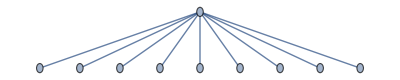
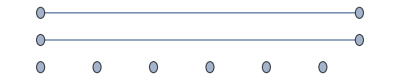
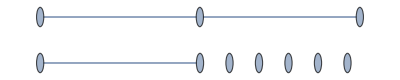
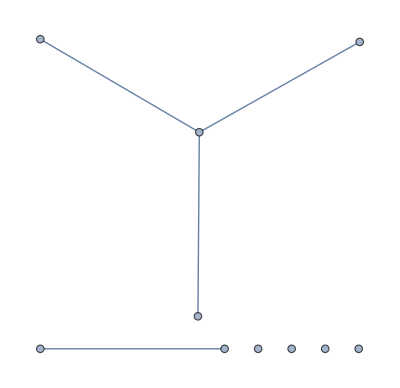
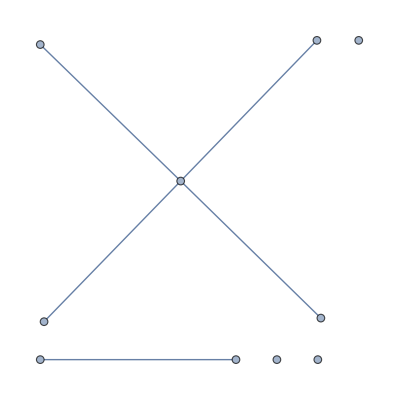
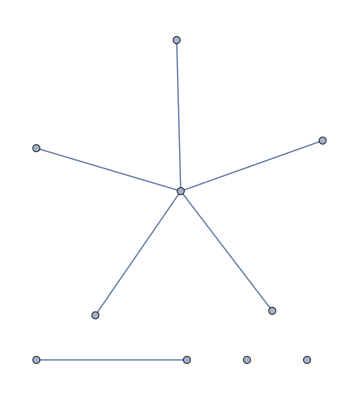

```mathematica
SimpleGraphs[10,10,15]
```

#### 多线程拆分

```mathematica
SetDirectory[NotebookDirectory[]];
ParallelNeeds["Extremal`"];
```

```mathematica
LaunchKernels[50];
$KernelCount
```

150

```mathematica
ClearAll[lock];
SetSharedVariable[size,step,n,medge,graphs,forbidden];
Needs["Extremal`"]
(*size of simple graphs of n vertices*)
forbidden=GraphF[2];
{n,size}={9,274668};
(*{n,size}={8,12346};*)
step=10^3;
(*output results*)
medge=0;
graphs={};
```

```mathematica
ChkPart[k_]:=Module[{edge=medge,newgraphs,a,b},
{a,b}={(k-1) step+1,k step};
If[a>size,Return[Nothing]];
If[b>size,b=size];
{newgraphs,edge}=ExtremalGraphs[SimpleGraphs[n,a,b],forbidden,edge];
CriticalSection[lock,Which[
edge<medge,Return[Nothing],
edge>medge,medge=edge;graphs=newgraphs,
edge==medge,medge=edge;graphs=Join[graphs,newgraphs]]];Nothing]
```

```mathematica
ParallelMap[ChkPart,Range@13]
```

15{9,1,1000,1}

16{9,1001,2000,2}

19{9,2001,3000,3}

14{9,3001,4000,4}

14{9,4001,5000,5}

15{9,5001,6000,6}

17{9,6001,7000,7}

14{9,7001,8000,8}

15{9,8001,9000,9}

16{9,9001,10000,10}

17{9,10001,11000,11}

19{9,11001,12000,12}

16{9,12001,13000,13}

1515

1616

1414

1414

1919

1717

1515

1414

1616

1515

1717

1919

1616

{}